# 微积分

## 梯度向量

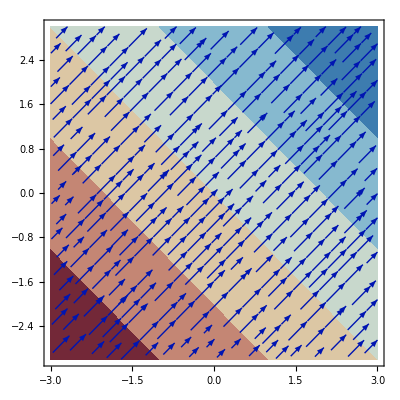
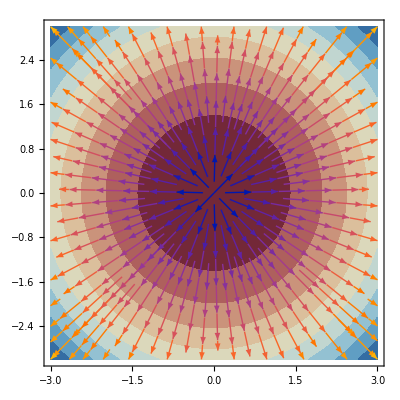
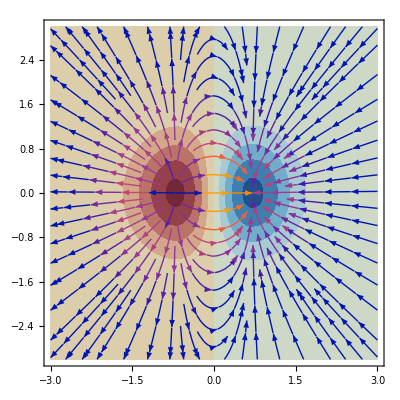

```mathematica
ContourPlot[#,{x1,-3,3},{x2,-3,3},ContourStyle->None,Epilog->First@StreamPlot[Evaluate@Grad[#,{x1,x2}],{x1,-3,3},{x2,-3,3}],ColorFunction->"RedBlueTones",PlotRange->All]&/@{x1+x2,x1^2+x2^2,x1 Exp[-(x1^2+x2^2)]}
```

## 法向量

```mathematica
SliceVectorPlot3D[Evaluate@Grad[x1 Exp[-(x1^2+x2^2)]-y,{x1,x2,y}],{x1 Exp[-(x1^2+x2^2)]-y==0},{x1,-3,3},{x2,-3,3},{y,-2,2},PlotTheme->"Scientific",Axes->False]
```

-Graphics3D-

## 二元线性逼近

```mathematica
Plot3D[{#,Evaluate@Normal@Series[#,{x1,0,1},{x2,-1.5,1}]},{x1,-2,2},{x2,-2,2},PlotRange->All,PlotTheme->"Minimal"]&[-4(x1^2+x2^2)]
```

-Graphics3D-

## 拉格朗日乘数法

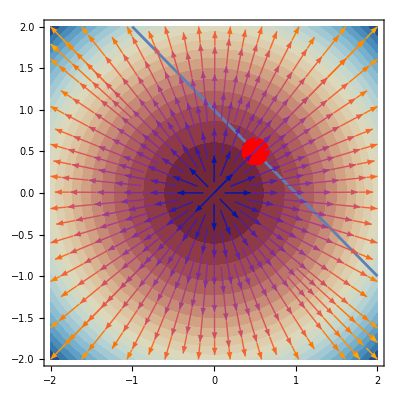
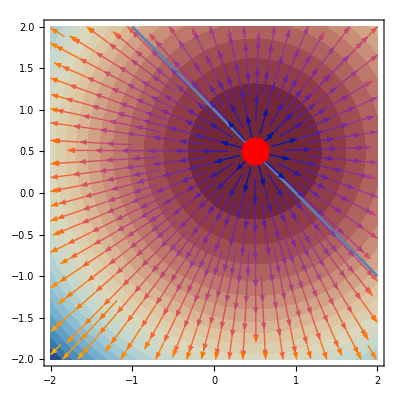

```mathematica
(*f(x)等高线与约束h(x)相切处，即为拉格朗日函数极值*)
(*线性等式约束*)
Show[ContourPlot[#,{x1,-2,2},{x2,-2,2},ContourStyle->None,Contours->20,Epilog->First@StreamPlot[Evaluate@Grad[#,{x1,x2}],{x1,-2,2},{x2,-2,2}],ColorFunction->"RedBlueTones",PlotRange->All],ContourPlot[x1+x2==1,{x1,-2,2},{x2,-2,2}],Graphics[{Red,PointSize[0.05],Point[FindMinimum[{x1^2+x2^2,x1+x2==1},{x1,x2}](*求得极小值点*)[[2,{1,2},2]](*取坐标*)]}]]&/@{x1^2+x2^2,x1^2+x2^2-(x1+x2-1)}
```

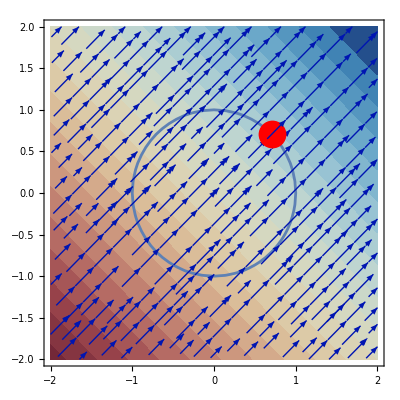
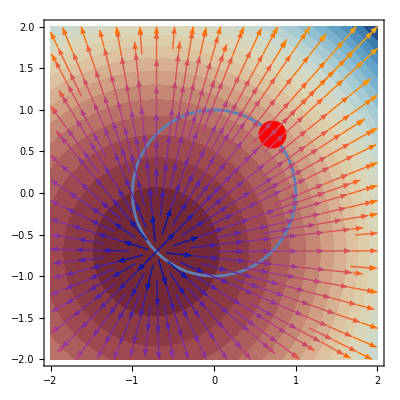

```mathematica
(*非线性等式约束*)
Show[ContourPlot[#,{x1,-2,2},{x2,-2,2},ContourStyle->None,Contours->20,Epilog->First@StreamPlot[Evaluate@Grad[#,{x1,x2}],{x1,-2,2},{x2,-2,2}],ColorFunction->"RedBlueTones",PlotRange->All],ContourPlot[x1^2+x2^2==1,{x1,-2,2},{x2,-2,2}],Graphics[{Red,PointSize[0.05],Point[FindMinimum[{x1+x2,x1^2+x2^2==1},{x1,x2}][[2,{1,2},2]]]}]]&/@{x1+x2,x1+x2+1/Sqrt[2](x1^2+x2^2-1)}
```

## 矩阵范数

矩阵1-范数：列元素绝对值之和最大范数 

矩阵∞-范数：行元素绝对值之和最大范数 

矩阵2-范数

矩阵F-范数

```mathematica
Norm[{{0,1},{1,1},{1,0}},#]&/@{1,Infinity,2,"Frobenius"}
```

{2,2,√3,2}